## Dynamic programming :

This is code by David B . Wagner for the Dynamic Programming

```mathematica
fib[n_]:= fib[n-1] + fib[n-2]
fib[0] = fib[1] = 1;
```

```mathematica
Array[fib, 8]
```

{1,2,3,5,8,13,21,34}

```mathematica
t=Table[Timing[fib[n]],{n,1,22}]
```

{{0.,1},{0.,2},{0.,3},{0.,5},{0.,8},{0.,13},{0.,21},{0.,34},{0.,55},{0.,89},{0.,144},{0.,233},{0.,377},{0.,610},{0.,987},{0.,1597},{0.015625,2584},{0.,4181},{0.,6765},{0.015625,10946},{0.03125,17711},{0.03125,28657}}

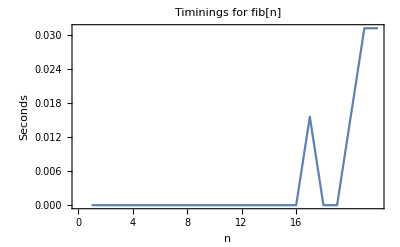

```mathematica
ListPlot[t[[All,1]], Joined->True, 
PlotLabel->"Timinings for fib[n]",
Frame->True, FrameLabel->{"n", "Seconds"},
FrameTicks->{Range[0,16,2], Automatic}]
```

```mathematica
Trace[fib[4], fib[_]]
```

{fib[4],{fib[3],{fib[2],{fib[1]},{fib[0]}},{fib[1]}},{fib[2],{fib[1]},{fib[0]}}}

```mathematica
Table[Count[Flatten[Trace[fib[i], fib[_]]],
HoldForm[fib[1]]],
{i,1,12}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

Performing computation bottom up and use results of smaller arguments to calculate the bigger arguments:

```mathematica
bufib[n_]:= Nest[{#[[2]], Plus@@ #}&, {0,1},n][[2]]
```

```mathematica
Table[bufib[n], {n,0,11}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

```mathematica
Clear[fib]
fib[n_]:= fib[n]= fib[n-1] + fib[n-2]
fib[0] = fib[1] = 1;
?fib
```

```mathematica
fib[3]
```

3

```mathematica
?fib
```

```mathematica
Timing[fib[100]]
```

{0.,573147844013817084101}

## Matrix Chain multiplication:

```mathematica
b1 = Table[Random[], {300},{10}];
b2 = Table[Random[], {10},{300}];
b3 = Table[Random[],{300},{10}];
```

```mathematica
b1.b2.b3; //Timing
```

{0.,Null}

Recurrence equation for m(i,j):

```mathematica
m[i_,j_]/; i <j := m[i,j]=
Min[Table[
m[i,k] + m[k+1,j]+p[[i]] p[[k+1]] p[[j+1]],
{k,i,j-1}]]
m[__]=0
```

0

Dimension of the matrices in the chain:

```mathematica
p = {30,35,15,5,10,20,25};
```

```mathematica
m[1,6]
```

15125

```mathematica
TableForm[
Array[m,{5,6}],
TableHeadings->Automatic,
TableAlignments->{Center, Right}]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | 0 | 15750 | 7875 | 9375 | 11875 | 15125
2 | 0 | 0 | 2625 | 4375 | 7125 | 10500
3 | 0 | 0 | 0 | 750 | 2500 | 5375
4 | 0 | 0 | 0 | 0 | 1000 | 3500
5 | 0 | 0 | 0 | 0 | 0 | 5000

```mathematica
Clear[m]
```

```mathematica
m[i_,j_]/; i <j:= m[i,j]=
Module[{choices, best},
choices = 
Table[m[i,k]+m[k+1,j]+
p[[i]] p[[k+1]] p[[j+1]],
{k,i,j-1}];
best=Min[choices];
s[i,j]=Position[choices,best][[1,1]]+i-1;
best]
m[__]:=0
```